```mathematica
depthToNQ[ depth_ ]:= 1 + Sum[ 2 * 2^k , {k,1,depth}];
diameterToDepth[ diam_ ] := diam/2 - 1;

binTreeGap[ diam_ ]:= Module[{g0, g1, ev0, ev1},
g0 =  DiagonalMatrix[ Join @@ ConstantArray[ { 1, 2 }, Floor[diam/2] ] , +1 ] + DiagonalMatrix[ ConstantArray[ 1, diam-1 ] , -1];
g1 = g0[[;;-2, ;;-2]];

ev0 = Sort[ Eigenvalues[ N@g0 ]   ][[  Ceiling[ diam/ 2 ]  + 1 ]];
ev1 = Sort[ Eigenvalues[ N@g1 ]   ][[  Floor[ diam/ 2 ]  + 1 ]];
Return[{depthToNQ@diameterToDepth[ diam ], Min[ ev0, ev1 ]  }]
];
```

```mathematica
diameters = Range[ 3, 20, 2  ];
treegapscaling = Table[ binTreeGap[ diam ], {diam, diameters} ]
```

{{1,1.},{5,0.517638},{13,0.311108},{29,0.200777},{61,0.134632},{125,0.0922773},{253,0.0640671},{509,0.0448218},{1021,0.0314994}}

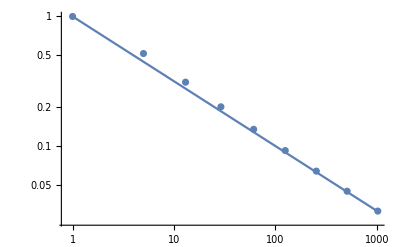

```mathematica
Show[{
ListLogLogPlot[res ]
, LogLogPlot[ x^-(1/2), {x,0,1000} ]
}]
```

## testing failure of det(G-p)!=0

```mathematica
mat = ({{0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0}, {0, 1, -1, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0}, {0, 1, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0, 0}})
```

{{0,0,0,0,0,0,0},{1,0,0,0,0,0,0},{1,0,0,0,0,0,0},{0,1,-1,0,0,0,0},{0,0,0,1,0,0,0},{0,1,0,0,1,0,0},{0,0,0,0,1,0,0}}

```mathematica
mat = mat + Transpose[mat];
```

```mathematica
mat // MatrixForm
```

(0 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 1 | -1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
mat // Eigensystem // N // Transpose //  MatrixForm
```

(-2.2725 | {0.608078,-2.10003,0.71818,2.24014,-2.2725,1.92411,1.}
2.2725 | {0.608078,2.10003,-0.71818,2.24014,2.2725,1.92411,1.}
-1.49236 | {-6.99045,3.86188,6.57038,2.81491,-1.49236,-1.58777,1.}
1.49236 | {-6.99045,-3.86188,-6.57038,2.81491,1.49236,-1.58777,1.}
0.780139 | {-0.117627,-0.652459,0.560694,-0.555046,0.780139,0.163664,1.}
-0.780139 | {-0.117627,0.652459,-0.560694,-0.555046,-0.780139,0.163664,1.}
0. | {1.,0.,0.,1.,0.,-2.,1.})

```mathematica
mat[[2;;, 2;; ]] // Eigensystem // N  //Transpose // MatrixForm
```

(-2.24698 | {-1.80194,1.,2.24698,-2.24698,1.80194,1.}
2.24698 | {1.80194,-1.,2.24698,2.24698,1.80194,1.}
0.801938 | {-0.445042,1.,-0.801938,0.801938,0.445042,1.}
-0.801938 | {0.445042,-1.,-0.801938,-0.801938,0.445042,1.}
-0.554958 | {1.24698,1.,0.554958,-0.554958,-1.24698,1.}
0.554958 | {-1.24698,-1.,0.554958,0.554958,-1.24698,1.})